# MÉTODOS COMPUTACIONALES EN ÓPTICA INTRODUCCIÓN AL PROGRAMA MATHEMATICA 4.2 TRANSFORMADA DE FOURIER NUMÉRICA (DISCRETA)

# Ejercicio 2. Propagación de pulsos

Vas a simular la propagación de un pulso ultracorto a través de un material. Para ello, parte del pulso del Ejemplo 1, tomando w=2*Pi*c/λ (siendo λ=0.8 micras y c=0.3 micras/fs) y b=2.  

a) Representa gráficamente el pulso y su intensidad espectral donde el eje de frecuencias aparezca en su orden “natural”, desde las negativas a las positivas

b) Estudia su propagación en el vacío. Para ello tienes que evaluar la transformada de Fourier inversa del campo en el espacio de frecuencias multiplicado por la fase correspondiente a su propagación como onda plana: exp(i k z), donde k=w/c (esta w es la variable, no la “w” central del pulso definida arriba), y z=7 micras. Ten cuidado con el orden de las frecuencias... Representalo gráficamente. ¿Qué le ocurre al pulso? Prueba a cambiar el valor de z.

c) Estudia su propagación en un material cuya relación de dispersión de Sellmeier es n(w)=Sqrt( 1 - 50/(w^2-6^2) ). Ahora la fase es: exp(i k n(w) z). Representa gráficamente. ¿Qué le sucede?

## a) Representa gráficamente el pulso y su intensidad espectral donde el eje de frecuencias aparezca en su orden “natural”, desde las negativas a las positivas.

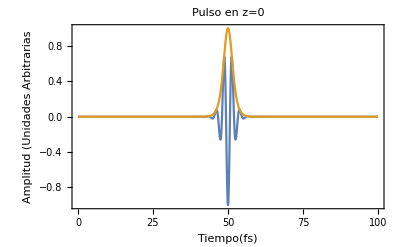

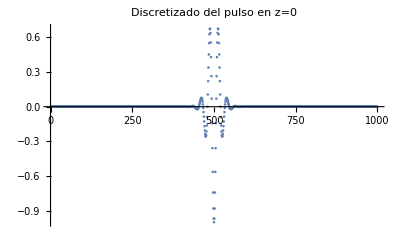

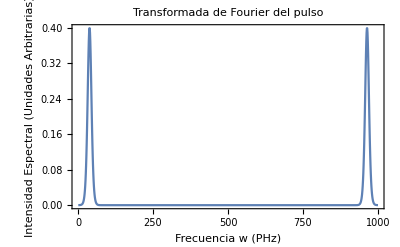

```mathematica
lan=0.8;
c=0.3;
b=2;
w=2*Pi*c/lan;
f[t_]=Sech[1/b (-50+t)]^2( Sin[w*t]);
Plot[{f[t],Sech[1/b (-50+t)]^2},{t,0,100},PlotRange->All,Frame->True,FrameLabel->{"Tiempo(fs)","Amplitud (Unidades Arbitrarias"},LabelStyle->{FontFamily->"Helvetica",FontSize->12},PlotLabel->"Pulso en z=0"]

tmax=100;
dt=0.1 ;
l1=Table[f[t],{t,dt,tmax,dt}];
 ListPlot[l1,PlotRange->All,PlotLabel->"Discretizado del pulso en z=0"]

np=Length[l1];
ftl1=Fourier[l1];
ListPlot[Re[ftl1*Conjugate[ftl1]],PlotRange->All,Frame->True,FrameLabel->{"Frecuencia w (PHz)","Intensidad Espectral (Unidades Arbitrarias)"},LabelStyle->{FontFamily->"Helvetica",FontSize->12},Axes->False,Joined->True,PlotLabel->"Transformada de Fourier del pulso"]
```

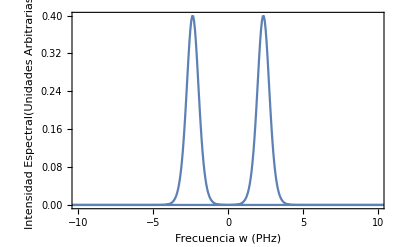

```mathematica
dw=2*Pi/(tmax);
wmax=Pi/dt;
wp=Table[(i-1)*dw,{i,1,np/2}];
wn=Table[-wmax+(i-1)*dw,{i,1,np/2}];
w=Join[wp,wn];
wft1=Table[{w[[i]],Re[ftl1[[i]]*Conjugate[ftl1[[i]]]]},{i,1,np}];
ListPlot[wft1,PlotRange->{{-10,10},All},Joined->True,FrameLabel->{"Frecuencia w (PHz)","Intensidad Espectral(Unidades Arbitrarias)"},Frame->True,Axes->False,LabelStyle->{FontFamily->"Helvetica",FontSize->12}]
```

# b) Estudia su propagación en el vacío. Para ello tienes que evaluar la transformada de Fourier inversa del campo en el espacio de frecuencias multiplicado por la fase correspondiente a su propagación como onda plana: exp(i k z), donde k=w/c (esta w es la variable, no la “w” central del pulso definida arriba), y z=7 micras. Ten cuidado con el orden de las frecuencias... Representalo gráficamente. ¿Qué le ocurre al pulso? Prueba a cambiar el valor de z.

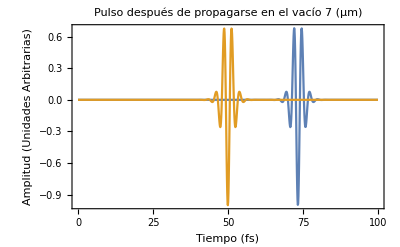

```mathematica
z=7;
ffase=Table[ftl1[[i]]*Exp[I*(w[[i]]/c)*z],{i,1,np}];
iffase=InverseFourier[ffase];
ListPlot[{Re[iffase],l1},PlotRange->All,DataRange->{0,100},Frame->True,FrameLabel->{"Tiempo (fs)","Amplitud (Unidades Arbitrarias)"},LabelStyle->{FontFamily->"Helvetica",FontSize->12},Joined->True,PlotLabel->"Pulso después de propagarse en el vacío 7 (μm)"]
```

El pulso sufre un desplazamiento temporal. Puede observarse como el centro del pulso pasa de estar en 50 fs a localizarse en torno a 75 fs. Por otra parte, no sufre ninguna deformación al propagarse en vacío.

# c) Estudia su propagación en un material cuya relación de dispersión de Sellmeier es n(w)=Sqrt( 1 - 50/(w^2-6^2) ). Ahora la fase es: exp(i k n(w) z). Representa gráficamente. ¿Qué le sucede?

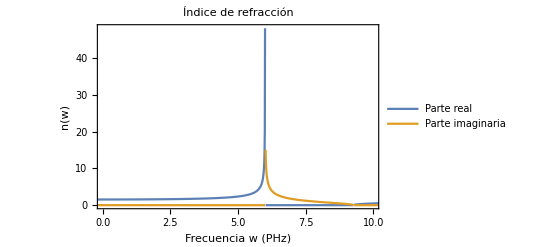

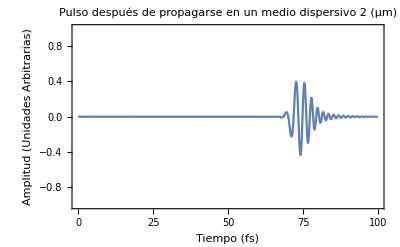

```mathematica
n[w_]:=Sqrt[1-50/(w^2-6^2)];
z=4;
k[w_]:=w/c;
Plot[{Re[n[w]],Im[n[w]]},{w,-wmax/2,wmax/2},PlotRange->{{0,10}, All},LabelStyle->{FontFamily->"Helvetica",FontSize->12},PlotLegends->{"Parte real","Parte imaginaria"},
Frame->True,FrameLabel->{"Frecuencia w (PHz)","n(w)"},PlotLabel->"Índice de refracción"]
wft2=Table[ftl1[[i]]*Exp[I*Sqrt[1-50*(w[[i]]^2-6^2-I*w[[i]]*0.1)/((w[[i]]^2-6^2)^2+w[[i]]^2*0.1^2)]*(w[[i]]/c)*z],{i,1,np-1}];

iffasev2=InverseFourier[wft2];
a=ListPlot[Re[iffasev2],PlotRange->{All, {-1,1}}, DataRange->{0,tmax},Frame->True,FrameLabel->{"Tiempo (fs)","Amplitud (Unidades Arbitrarias)"},LabelStyle->{FontFamily->"Helvetica",FontSize->10},Joined->True,PlotLabel->"Pulso después de propagarse en un medio dispersivo 2 (μm)"]
```

En este medio la frecuencia de resonancia (6 PHz) es próxima a las frecuencias con las que estamos trabajando, por ello, algunas de las frecuencias se absorberán y el máximo de amplitud que registramos es menor que en el caso de propagarse por el vacío. Además  el índice de refracción depende de la longitud de onda. En esta situación el pulso se ensancha  al propagarse, decimos que el pulso adquiere un chirp positivo: primero aparecen las frecuencias bajas y posteriormente las frecuencias altas.